```mathematica
(**************************)

Gruzberg Mirlin

(*************************)
```

```mathematica
(* codice con correzioni al secondo ordine *)
(*
IteraSolve2:=(
Pite={};
dsol={};
dmaxite={};
dmax=1.;
While[dmax>10^-10,

nψ[-Lm]=   E^(H/(-1+m));
Do[
int=0;
int=1/4 E^J E^(H/(-1+m))  (1-H^2 E^(-2 t))( J E^t/H)^2 Exp[-J  E^t/H];
(* questo è il contributo all'integrale che viene da tt=0, è moltiplicato per 1/2, per ricavarlo si usa il limite della Bessel per argomento nullo, dall'altra parte invece non dovrei avere problemi *)
Do[

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2 tende a zero per x che diverge, cioe' H piccolo *)
,{tt,-Lm+dt,LM,dt}];
nψ[t]=   Exp[J-J E^t/H] E^(H/(-1+m))+   int dt;,{t,-Lm+dt,LM,dt}];
Do[diffψ[t]=ψ[t]-nψ[t];,{t,-Lm,LM,dt}];


dmax=Max[Table[Abs[diffψ[t]],{t,-Lm,LM,dt}]];
AppendTo[dsol,Table[{tt,diffψ[tt]/dmax},{tt,-Lm,LM,dt}]];
AppendTo[dmaxite,dmax];

Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];

P=0;
Do[P+=ψ[t]^(m+1) E^(- E^t) E^t ,{t,-Lm,LM,dt}];
P*=(dt); (* controllare la formula, manca un pezzo che dovrebbe dare correzioni regolari in H  *)
AppendTo[Pite,P];


])
*)
```

```mathematica
(* con le formule scritte come sopra e' immediato fare il limite per H=0 analiticamente *)
```

```mathematica
(* codice ancora piu' preciso con le somme (3/8,7/6,23/24) ha correzioni al quarto ordine dt^4 *)
```

```mathematica
(*

IteraSolve:=(
Pite={};
dsol={};
dmaxite={};
dmax=1.;
While[dmax>10^-10,

nψ[-Lm]=   E^(H/(-1+m));
Do[
int=0;
int=3/16 E^J E^(H/(-1+m))  (1-H^2 E^(-2 t))( J E^t/H)^2 Exp[-J  E^t/H];
(* questo è il contributo all'integrale che viene da tt=-Lm, è moltiplicato per 3/8, per ricavarlo si usa il limite della Bessel per argomento nullo, dall'altra parte invece non dovrei avere problemi *)

tt=-Lm+dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=7/6(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+dt, è moltiplicato per 7/6 *)

tt=-Lm+2dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=23/24(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+2 , è moltiplicato per 23/24  *)
tt=.;
Do[

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2 tende a zero per x che diverge, cioe' H piccolo *)
,{tt,-Lm+3dt,LM,dt}];
nψ[t]=   Exp[J-J E^t/H] E^(H/(-1+m))+   int dt;,{t,-Lm+dt,LM,dt}];
Do[diffψ[t]=ψ[t]-nψ[t];,{t,-Lm,LM,dt}];


dmax=Max[Table[Abs[diffψ[t]],{t,-Lm,LM,dt}]];
AppendTo[dsol,Table[{tt,diffψ[tt]/dmax},{tt,-Lm,LM,dt}]];
AppendTo[dmaxite,dmax];

Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];

P=0;
Do[P+=ψ[t]^(m+1) E^(- E^t) E^t ,{t,-Lm,LM,dt}];
P*=(dt); (* controllare la formula, manca un pezzo che dovrebbe dare correzioni regolari in H  *)
AppendTo[Pite,P];


])
```

```mathematica
(* codice ancora piu' preciso con le somme sui primi cinque termini ha correzioni all'ordine dt^6 *)
```

```mathematica
IteraSolve:=(
Pite={};
dsol={};
dmaxite={};
dmax=1.;
While[dmax>10^-10,

nψ[-Lm]=   E^(H/(-1+m));
Do[
int=0;
int=95/288 1/2 E^J E^(H/(-1+m))  (1-H^2 E^(-2 t))( J E^t/H)^2 Exp[-J  E^t/H];
(* questo è il contributo all'integrale che viene da tt=-Lm, è moltiplicato per 281/720, per ricavarlo si usa il limite della Bessel per argomento nullo, dall'altra parte invece non dovrei avere problemi *)

tt=-Lm+dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=317/240(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+dt, è moltiplicato per 1057/720 *)

tt=-Lm+2dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=23/30(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+2 , è moltiplicato per ...  *)
tt=.;


tt=-Lm+3dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=793/720(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+3 , è moltiplicato per ...  *)
tt=.;


tt=-Lm+4dt;

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=157/160(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* questo è il contributo all'integrale che viene da tt=-Lm+4 , è moltiplicato per ...  *)
tt=.;





Do[

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2 tende a zero per x che diverge, cioe' H piccolo *)
,{tt,-Lm+5dt,LM,dt}];
nψ[t]=   Exp[J-J E^t/H] E^(H/(-1+m))+   int dt;,{t,-Lm+dt,LM,dt}];
Do[diffψ[t]=ψ[t]-nψ[t];,{t,-Lm,LM,dt}];


dmax=Max[Table[Abs[diffψ[t]],{t,-Lm,LM,dt}]];
AppendTo[dsol,Table[{tt,diffψ[tt]/dmax},{tt,-Lm,LM,dt}]];
AppendTo[dmaxite,dmax];

Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];

P=0;
Do[P+=ψ[t]^(m+1) E^(- E^t) E^t ,{t,-Lm,LM,dt}];
P*=(dt); (* controllare la formula, manca un pezzo che dovrebbe dare correzioni regolari in H  *)
AppendTo[Pite,P];


])
```

```mathematica
(** parametri equazioni *)
m=2;

dtt=0.08; (* dt target *)

(* parametri soluzione numerica *)

(* NN=100; *) 

Lm=6;
LM=10;

NN=IntegerPart[Lm/dtt] (* prendo NN in modo da avviciarmi al dt target *)

dt=Lm/NN; (* fondamentale deve essere un razionale, altrimenti non funziona come indici !!!! *)
N[dt]

H=N[E^-Lm]
J=.01;


(* condizione iniziale *)
Do[nψ[tt]= E^(H/(m-1))Chop[E^(- E^tt)],{tt,-Lm,LM,dt}];

(* condizione iniziale costante *)
(*
Do[nψ[tt]= E^(H/(m-1))1.,{tt,-Lm,LM,dt}];
Do[nψ[tt]= 0.,{tt,-Lm,LM,dt}];
*)
Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];
```

75

0.08

0.00247875

General::munfl: Exp[-765.095] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-828.818] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-897.847] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
IteraSolve[];
```

General::munfl: 8.97947×10^-273 6.81599×10^-58 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.04218×10^-295 1.18114×10^-62 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.73184×10^-136 9.19978×10^-184 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
lisψ6p08=Table[{t,N[ψ[t]]},{t,-Lm,LM,dt}];
```

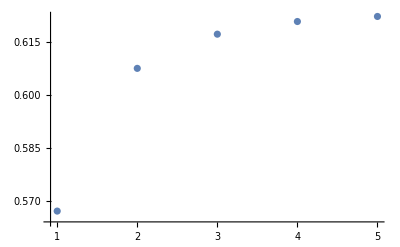

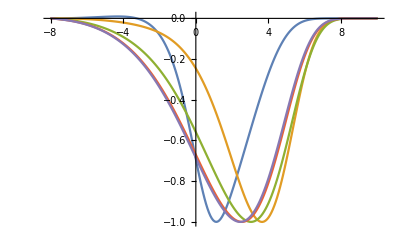

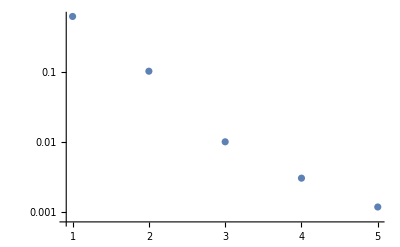

```mathematica
ListPlot[Pite,PlotRange->All]
ListPlot[dsol,PlotRange->All,Joined->True]
ListLogPlot[dmaxite,PlotRange->All]
```

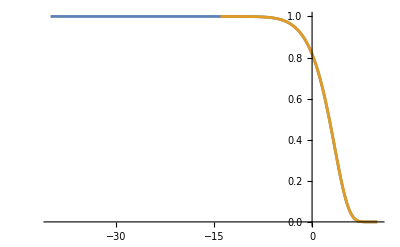

```mathematica
ListPlot[{lisψ0,lisψ14p08},PlotRange->All,Joined->True]
```

```mathematica
(* risultati con il codice nuovo, con il vecchio venivano i bozzi  *)
```

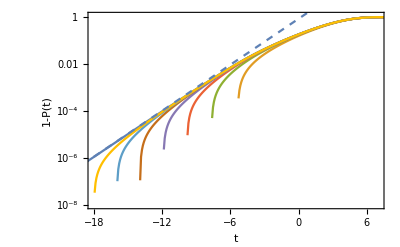

```mathematica
Show[ListLogPlot[{Map[{#[[1]],1-#[[2]]}&,lisψ0],Map[{#[[1]],1-#[[2]]}&,lisψ6p08],Map[{#[[1]],1-#[[2]]}&,lisψ8p08],Map[{#[[1]],1-#[[2]]}&,lisψ10p08],Map[{#[[1]],1-#[[2]]}&,lisψ12p08],Map[{#[[1]],1-#[[2]]}&,lisψ14p08],Map[{#[[1]],1-#[[2]]}&,lisψ16p08],Map[{#[[1]],1-#[[2]]}&,lisψ18p08]},PlotRange->{{-18,7},{10^-8,1.1}},Joined->True,Frame->True,FrameLabel->{Style["t",Italic],Style["1-P(t)",Italic]}],LogPlot[.8525 E^(0.7530159246380487  t),{t,-20,1},PlotStyle->{Dashed}]]
```

```mathematica
(*
lisψ0>>lisψ0;

lisψ18p08>>lisψ18p08;
lisψ16p08>>lisψ16p08;
lisψ14p08>>lisψ14p08;
lisψ12p08>>lisψ12p08;
lisψ10p08>>lisψ10p08;
lisψ8p08>>lisψ8p08;
lisψ6p08>>lisψ6p08;

*)
```

```mathematica
(*******************************************************)
(*******************************************************)
(******** differenza con la soluzione a H=0 ************)
(*******************************************************)
(*******************************************************)
(*******************************************************)
```

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.7513

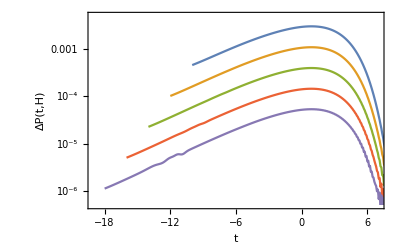

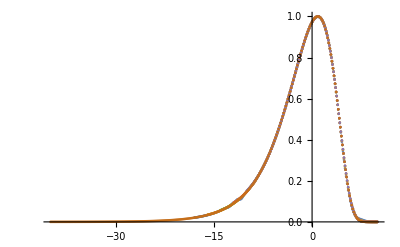

```mathematica
lismax={};

lis=lisψ18p08;
d18=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[lisψ0][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d18;
mm=Max[Map[#[[2]]&,dd]];
AppendTo[lismax,{E^-18,mm}];
sd18=Map[{#[[1]],#[[2]]/mm}&,dd];

lis=lisψ16p08;
d16=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[lisψ0][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d16;
mm=Max[Map[#[[2]]&,dd]];
AppendTo[lismax,{E^-16,mm}];
sd16=Map[{#[[1]],#[[2]]/mm}&,dd];


lis=lisψ14p08;
d14=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[lisψ0][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d14;
mm=Max[Map[#[[2]]&,dd]];
AppendTo[lismax,{E^-14,mm}];
sd14=Map[{#[[1]],#[[2]]/mm}&,dd];

lis=lisψ12p08;
d12=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[lisψ0][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d12;
mm=Max[Map[#[[2]]&,dd]];
AppendTo[lismax,{E^-12,mm}];
sd12=Map[{#[[1]],#[[2]]/mm}&,dd];



lis=lisψ10p08;
d10=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[lisψ0][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d10;
mm=Max[Map[#[[2]]&,dd]];
AppendTo[lismax,{E^-10,mm}];
sd10=Map[{#[[1]],#[[2]]/mm}&,dd];


dd=lisdψ0;
mm=Max[Map[#[[2]]&,dd]];
slisdψ0=Map[{#[[1]],#[[2]]/mm}&,dd];
1/mm



ListLogPlot[{d10,d12,d14,d16,d18},PlotRange->{{-19,7},{.5 10^-6,.005}},Joined->True,Frame->True,FrameLabel->{Style["t",Italic],Style["ΔP(t,H)",Italic]}]
ListPlot[{sd18,sd16,sd14,sd12,sd10,slisdψ0},PlotRange->All]
```

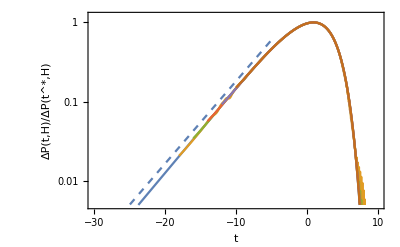

1.7513

```mathematica
Show[ListLogPlot[{slisdψ0,sd18,sd16,sd14,sd12,sd10},PlotRange->{{-30,10},{.005,1.2}},Joined->True,Frame->True,FrameLabel->{Style["t",Italic],Style["ΔP(t,H)/ΔP(t^*,H)",Italic]}],LogPlot[2. E^(.24 zz),{zz,-30,-5},PlotStyle->Dashed]]
```

```mathematica
la curva decresce come   C(H)E^((1-b)t)  questa per t =-Lm deve essere uguale a c E^(b t), segue che   C(H)== c E^(-b Lm+(1-b)Lm)=c H^(1-2 b)
```

```mathematica
perfetto, si vede che la curva si mette perfettamente  sulla soluzione delle equazioni linearizzate che decresce con E^((1-b)t)
```

```mathematica
Lo studio della linearizzata per t e vicino al lower bound anche mostra che diverge a grandi t come  E^(b tt)-cc E^((1-b) tt) : questo completa l'analisi di quello che serve per calcolare tutto, quindi il risultato finale dipende dalle variabili c, cc e dall'integrale della soluzione delle equazioni linearizzate che decresce con E^((1-b)t)
```

```mathematica
(*********************************************************)
(*********************************************************)(*********************************************************)(***********Analisi dell'errore               ************)(*********************************************************)(*********************************************************)(*********************************************************)
```

```mathematica
(************ il codice ha delle correzioni dt^4 come deve, per calcolare, paragonano le soluzioni con Lm=6 e dt=.08,.04,.02, se necessario puoi fare le estrapolazioni   *************)
```

```mathematica
Length[lisψ6ncp08]
Length[lisψ6ncp04]
Length[lisψ6ncp02]
```

201

401

801

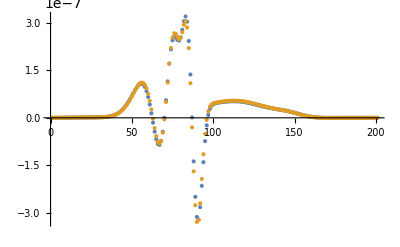

```mathematica
ListPlot[{Table[{q,lisψ6ncp08[[q,2]]-lisψ6ncp04[[2q-1,2]]},{q,1,Length[lisψ6ncp08]}],Table[{q,16(lisψ6ncp04[[2q-1,2]]-lisψ6ncp02[[4q-3,2]])},{q,1,Length[lisψ6ncp08]}]},PlotRange->All]
```

{{0.00004096,0.724349},{2.56×10^-6,0.724349},{1.6×10^-7,0.724349}}

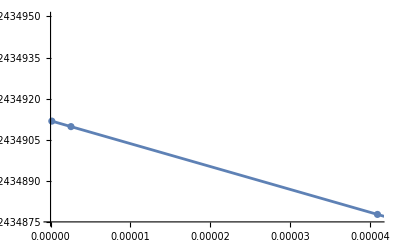

```mathematica
q=91;
dat={{(.08)^4,lisψ6ncp08[[q,2]]},{(.04)^4,lisψ6ncp04[[2q-1,2]]},{(.02)^4,lisψ6ncp02[[4q-3,2]]}}
fit=Fit[dat,{1,xx},xx];
Show[ListPlot[dat,PlotRange->{0.72434875,0.7243495}],Plot[fit,{xx,0,(.09)^4}]]
q=.
```

```mathematica
(************ il codice al secondo ordine ha delle correzioni dt^2 come deve *************)
```

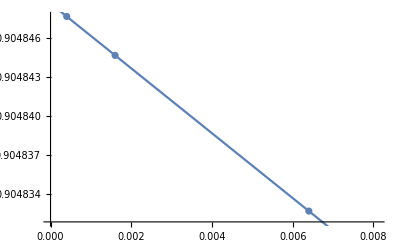

```mathematica
q=-1;

fit=Fit[{{(.02)^2,Interpolation[lisψ6p02][q]},{(.04)^2,Interpolation[lisψ6p04][q]},{(.08)^2,Interpolation[lisψ6p08][q]}},{1,xx},xx];
Show[ListPlot[{{(.02)^2,Interpolation[lisψ6p02][q]},{(.04)^2,Interpolation[lisψ6p04][q]},{(.08)^2,Interpolation[lisψ6p08][q]}},PlotRange->{{0,(.09)^2},Automatic}],Plot[fit,{xx,0,(.09)^2}]]
q=.
```

```mathematica
(* Il vecchio codice aveva delle correzioni di ordine dt *)
```

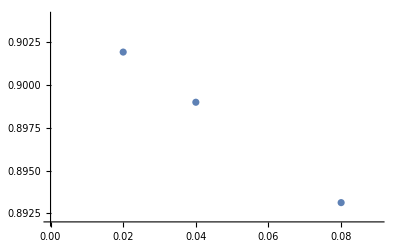

```mathematica
q=-1.;
ListPlot[{{.02,Interpolation[lisψ6p02][q]},{.04,Interpolation[lisψ6p04][q]},{.08,Interpolation[lisψ6p08][q]}},PlotRange->{{0,.09},{0.892,.904}}]
q=.
```

```mathematica
dif1=Table[{q,(Interpolation[lisψ6p04][q]-Interpolation[lisψ6p08][q])/(.08-.04)},{q,-6,10,.1}];
dif2=Table[{q,(Interpolation[lisψ6p02][q]-Interpolation[lisψ6p04][q])/(.04-.02)},{q,-6,10,.1}];
```

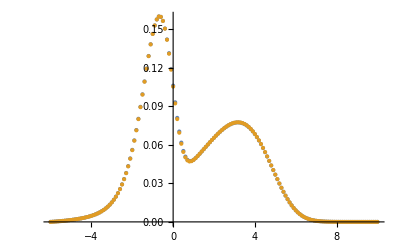

```mathematica
ListPlot[{dif1,dif2}]
```

```mathematica
(*********************************************************)
(*********************************************************)
(*********************************************************)
(*********************************************************)
(*********************************************************)
(*********************************************************)
(*********************************************************)
```

```mathematica
(* condizione di ν *)
```

```mathematica
FindRoot[BesselK[-1/2+ν,J]/BesselK[-1/2,J]==1/m,{ν,1.}]
```

{ν→0.753016}

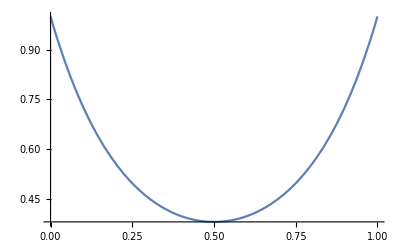

```mathematica
Plot[BesselK[-1/2+ν,J]/BesselK[-1/2,J],{ν,0,1}]
```

```mathematica
(* valore critico di J *)
```

```mathematica
J=.
FindRoot[BesselK[0,J]/BesselK[-1/2,J]==1/m,{J,.01}]
```

{J→0.0265402}

```mathematica
J=.
1/(2BesselK[-1/2,J])
```

(ⅇ^J √J)/(√(2 π))

General::munfl: Exp[-731.294] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-792.203] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-858.184] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

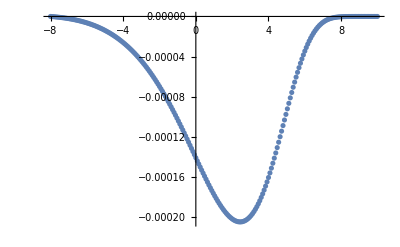

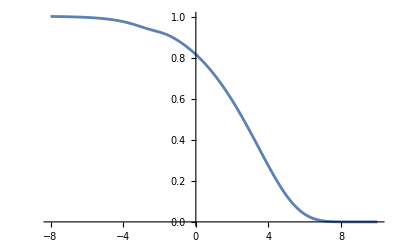

```mathematica
(* (* Codice con le formule esatte ma senza la trattazione accurata degli estremi *)

Do[
int=0;
Do[

If[Chop[Exp[J-J E^(t+tt)/H^2]]==0,
int+=ψ[tt]^m E^(-E^tt)(1-H^2 E^(-2 tt))^(-3/4)J (1-H^2 E^(-2 t))^(1/4)Exp[(t-tt)/2+J-1/2 ⅇ^(t-tt) J-1/2 ⅇ^(-t+tt) J-1/8 ⅇ^(t-3 tt) H^2 J+1/4 ⅇ^(-t-tt) H^2 J-1/8 ⅇ^(-3 t+tt) H^2 J]/(2 π J )^(1/2),
int+=ψ[tt]^m E^(-E^tt)(1-H^2 E^(-2 tt))^(-1/2)J E^t/H (1-H^2 E^(-2 t))^(1/2)Exp[J-J E^(t+tt)/H^2]BesselI[1,J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2)]];
,{tt,-Lm+dt,LM,dt}];
nψ[t]=   Exp[J-J E^t/H] E^(H/(-1+m))+   int dt;,{t,-Lm,LM,dt}];
Do[diffψ[t]=ψ[t]-nψ[t];,{t,-Lm,LM,dt}];
Do[ψ[t]=nψ[t],{t,-Lm,LM,dt}];
```

```mathematica
(*************************************************)
(* manipolazioni varie *)
(*************************************************)(*************************************************)(*************************************************)(*************************************************)(*************************************************)(*************************************************)
```

```mathematica
Clear[H,J]
```

```mathematica
-J E^(t+tt)/H^2+J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2)
```

```mathematica
-J E^(t+tt)(1-(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))/H^2
```

```mathematica
(1-(1-x)^(1/2)(1-y)^(1/2))(1+(1-x)^(1/2)(1-y)^(1/2))/(1+(1-x)^(1/2)(1-y)^(1/2))=x/(1+(1-x)^(1/2))
```

```mathematica
x=.
```

```mathematica
Expand[1-(1-x)(1-y)]
```

x+y-x y

```mathematica
-J E^(t+tt)(1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(-2 tt)+E^(-2 t)-H^2 E^(-2 t-2tt))
```

```mathematica
(** questa è y **)
```

```mathematica
J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2)-J E^(t+tt)/H^2=
```

```mathematica
J E^(t+tt)/H^2((1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2)-1)=J E^(t+tt)/H^2((1-H^2 E^(-2 tt))(1-H^2 E^(-2 t))-1)((1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))+1)^-1=-J (E^(t- tt)+E^(tt- t)-H^2 E^(- tt)E^(- t))((1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))+1)^-1
```

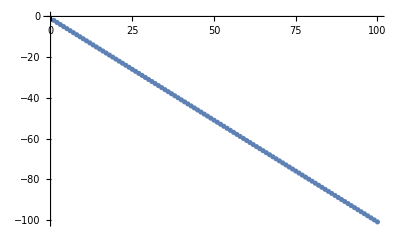

```mathematica
ListPlot[{Table[{lx,Log[-(Log[1-(3/8)/E^lx])]},{lx,1,100}]}]
```

```mathematica
Log[x]> 15  approssimiamo e non dovremmo avere problemi
```

```mathematica
Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2]
```

```mathematica
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
```

```mathematica
BesselI[1,0]
```

0

```mathematica
(*************************************************)
(*************************************************)
(*************************************************)
(*************************************************)
(*************************************************)
(*************************************************)
(******** Soluzione linearizzata  *************)
(*************************************************)
(*************************************************)
(*************************************************)
(*************************************************)
(*************************************************)
```

```mathematica
(* ok funzione la soluzione converge ad una soluzione che vale zero in zero (che corrisponde al valore minimo) e cresce esponenzialmente a grandi valori, la soluzione è di ordine H^b però quello che conta è il termine subleading. Infatti si impone che il comportamento a grandi tempi sia E^(b tt)-cc E^((1-b) tt) e si sceglie cc in modo tale da avere un qualcosa di smooth   *)
```

```mathematica
(** parametri equazioni *)
m=2;

(* parametri soluzione numerica *)

Lm=0; 
H=N[E^-Lm]; (* il campo è come se fosse uno *)
LM=40;
Δ=30;  (* valore oltre il quale impongo che la soluzione vada come E^(b tt) *)

NN=250; 

dt=LM/NN; (* fondamentale deve essere un razionale, altrimenti non funziona come indici !!!! *)
N[dt]

J=.01;

b=0.753015924638048;
cc=.969181;

(* condizione iniziale OK  *)
Do[nψ[tt]=E^(b tt)-cc E^((1-b) tt),{tt,-Lm,LM,dt}];
Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];
```

0.16

```mathematica
lisψlin0=Table[{tt,ψ[tt]},{tt,Lm,LM,dt}];
```

```mathematica
IteraSolveLin[];
```

General::munfl: Exp[-781.68] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-916.376] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1074.43] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

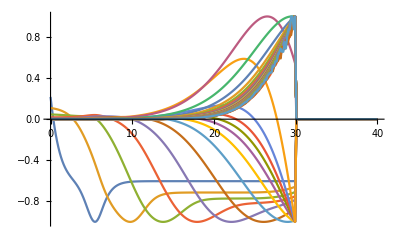

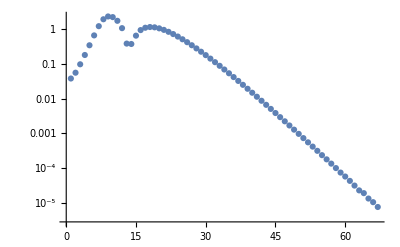

```mathematica
ListPlot[dsol,PlotRange->All,Joined->True]
ListLogPlot[dmaxite,PlotRange->All]
```

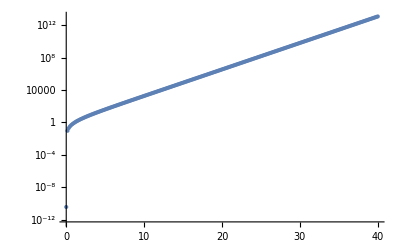

```mathematica
ListLogPlot[Table[{tt,ψ[tt]},{tt,Lm,LM,dt}],Joined->False,
PlotRange->All]
```

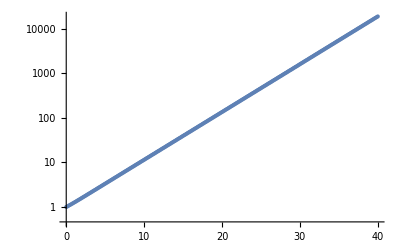

```mathematica
Show[ListLogPlot[Table[{tt,E^(b tt)-ψ[tt]},{tt,Lm,LM,dt}],Joined->False,
PlotRange->All],LogPlot[E^((1-b)t),{t,0,40}]]
```

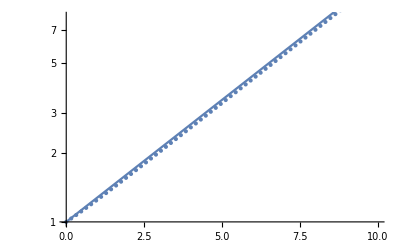

```mathematica
Show[ListLogPlot[Table[{tt,E^(b tt)-ψ[tt]},{tt,Lm,LM,dt}],Joined->False,
PlotRange->{{0,10},{1,8}}],LogPlot[E^((1-b)t),{t,0,40}]]
```

```mathematica
(* con il grafico qui sotto ho fissato cc, in modo tale che sia perfettamente piatto, se cambio cc curva intorno al boundary 30 *)
```

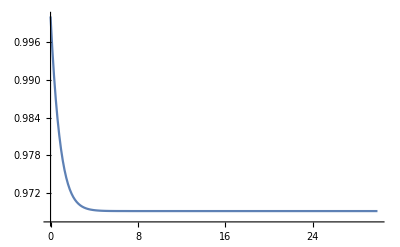

```mathematica
ListPlot[Table[{tt,(E^(b tt)-ψ[tt])/E^((1-b)tt)},{tt,Lm,Δ,dt}],PlotRange->All,Joined->True]
```

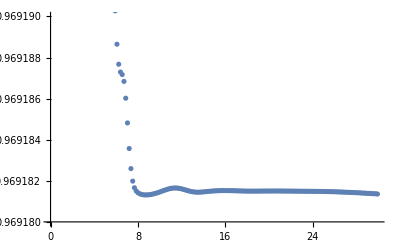

```mathematica
ListPlot[Table[{tt,(E^(b tt)-ψ[tt])/E^((1-b)tt)},{tt,Lm,Δ,dt}],{PlotRange->{.96918,.96919}}]
```

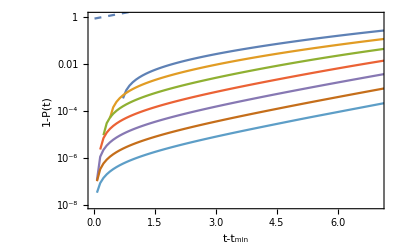

```mathematica
Show[ListLogPlot[{Map[{#[[1]]+6,1-#[[2]]}&,lisψ6p08],Map[{#[[1]]+8,1-#[[2]]}&,lisψ8p08],Map[{#[[1]]+10,1-#[[2]]}&,lisψ10p08],Map[{#[[1]]+12,1-#[[2]]}&,lisψ12p08],Map[{#[[1]]+14,1-#[[2]]}&,lisψ14p08],Map[{#[[1]]+16,1-#[[2]]}&,lisψ16p08],Map[{#[[1]]+18,1-#[[2]]}&,lisψ18p08]},PlotRange->{{0,7},{10^-8,1.1}},Joined->True,Frame->True,FrameLabel->{Style["t-t_min",Italic],Style["1-P(t)",Italic]}],LogPlot[.8525 E^(0.7530159246380487  t),{t,-20,1},PlotStyle->{Dashed}]]
```

```mathematica
Table[{tt,ψ[tt]},{tt,Lm,LM,dt}]
```

```mathematica
c
```

0.8525

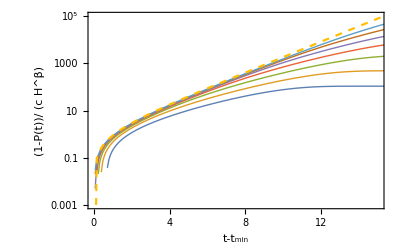

```mathematica
ListLogPlot[{Map[{#[[1]]+6,(1-#[[2]])/(c E^(-6 b))}&,lisψ6p08],Map[{#[[1]]+8,(1-#[[2]])/(c E^(-8 b))}&,lisψ8p08],Map[{#[[1]]+10,(1-#[[2]])/(c E^(-10 b))}&,lisψ10p08],Map[{#[[1]]+12,(1-#[[2]])/(c E^(-12 b))}&,lisψ12p08],Map[{#[[1]]+14,(1-#[[2]])/(c E^(-14 b))}&,lisψ14p08],Map[{#[[1]]+16,(1-#[[2]])/(c E^(-16 b))}&,lisψ16p08],Map[{#[[1]]+18,(1-#[[2]])/(c E^(-18 b)) }&,lisψ18p08],lisψlin0},PlotStyle->{Thick,Thick,Thick,Thick,Thick,Thick,Thick,Dashed},PlotRange->{{0,15},{.001,100000}},Joined->True,Frame->True,FrameLabel->{Style["t-t_min",Italic],Style["(1-P(t))/ (c H^β)",Italic]}]
```

```mathematica
IteraSolveLin:=(

dsol={};
dmaxite={};
dmax=1.;
While[dmax>10^-5,
nψ[-Lm]=   m  E^-H ψ[-Lm]; (* linearizziamo questo lo fa decrescere,  m  E^-H è minore di uno per H=1 *)
Do[
int=3/16 E^J m  ψ[-Lm]  (1-H^2 E^(-2 t))( J E^t/H)^2 Exp[-J  E^t/H];
(* contributo all'integrale in tt di di tt=-Lm, bisogna farlo usando il limite per la Bessel a x=0 *)

tt=-Lm+dt;
x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=7/6 m(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]  (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
tt=.;
(* contributo all'integrale in tt di di tt= -Lm+dt *)

tt=-Lm+2dt;
x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande *)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=23/24 m(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]  (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
tt=.;
(* contributo all'integrale in tt di di tt= -Lm+2 dt *)
Do[

x=J E^(t+tt)/H^2(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2);(* x e' l'argomento della BesselI che e' molto grande in general ma non in questo caso perchè t e tt sono finiti e H=1, correisponde al fatto che H è infinitesimo ma sono molto vicino al valore minimo di t e tt cioè  Log[H]*)
y=-J (1+(1-H^2 E^(-2 tt))^(1/2)(1-H^2 E^(-2 t))^(1/2))^-1(E^(t- tt)+E^(tt- t)-H^2 E^(- t-tt)) (* y ha un limite finito per H piccolo: tende  a -J Cosh[t-tt] *);
If[Log[x]<15, fac=Exp[Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2],fac=1-(3/8)/x];
(* sostituisco l'espansione asintotica quando x è troppo grande *)
int+=m(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]  (1-H^2 E^(-2 tt))^(-3/4)(1-H^2 E^(-2 t))^(1/4) Exp[(t-tt)/2+y]fac;
(* Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2 tende a zero per x che diverge, cioe' H piccolo *)
,{tt,-Lm+3dt,LM,dt}];
nψ[t]=  m  E^-H ψ[-Lm]+   int dt;,{t,-Lm+dt,LM,dt}];

Do[diffψ[t]=ψ[t]-nψ[t];,{t,-Lm,LM,dt}];

Do[If[t>Δ,nψ[t]= E^(b t)-cc E^((1-b) t);diffψ[t]=0.],{t,-Lm,LM,dt}]; (*fissiamo il limite *)
Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];


dmax=Max[Table[Abs[diffψ[t]],{t,-Lm,LM,dt}]];
AppendTo[dsol,Table[{tt,diffψ[tt]/dmax},{tt,-Lm,LM,dt}]];
AppendTo[dmaxite,dmax];




])
```

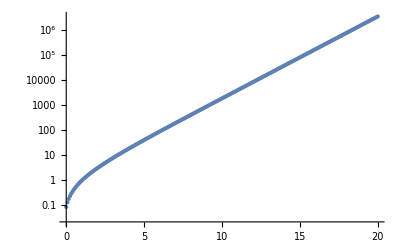

```mathematica
ListLogPlot[Table[{tt,ψ[tt]},{tt,Lm,LM,dt}],Joined->False,
PlotRange->All]
```

```mathematica
ψ[0]
```

0.0342051

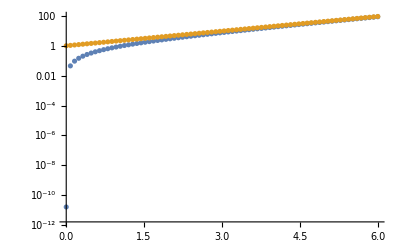

```mathematica
ListLogPlot[{Table[{tt,ψ[tt]},{tt,Lm,6,dt}],Table[{tt,E^(b tt)},{tt,Lm,6,dt}]},Joined->False,
PlotRange->All]
```

```mathematica
OK
```

```mathematica
la soluzione in 5 arriva al valore asintotico
dove la soluzione vale 1- c E^(b (-Lm+5)) dove questo è Lm vero, quindi il prefattore della soluzione è proprio  c E^(-b Lm)= c H^b
```

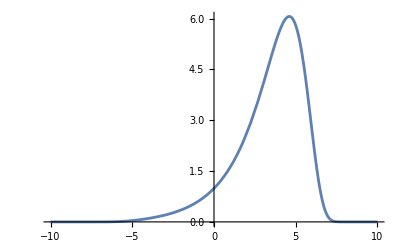

```mathematica
Plot[Exp[t/2-J Cosh[t]],{t,-10,10}]
```

```mathematica
Integrate[Exp[t/2-JJ Cosh[t]],{t,-∞,∞}]
```

ConditionalExpression[(ⅇ^-JJ √(2 π))/(√JJ), Re[JJ]>0]

```mathematica
(*************************************************)(*************************************************)(*************************************************)(**********************************************)
```

```mathematica
(*  Soluzione H=0 *)
```

```mathematica
(*************************************************)(*************************************************)(*************************************************)(*************************************************)(**********************************************)
```

```mathematica
(** parametri equazioni *)
m=2;


(* parametri soluzione numerica *)

Lm=40;
LM=10;

NN=250; 

dt=Lm/NN; (* fondamentale deve essere un razionale, altrimenti non funziona come indici !!!! *)
N[dt]


J=.01;


(* condizione iniziale *)
Do[nψ[tt]=Chop[E^(- E^tt)],{tt,-Lm,LM,dt}];

(* condizione iniziale costante *)

Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];
```

0.16

```mathematica
IteraSolve0:=(
Pite={};
dsol={};
dmaxite={};
dmax=1.;
While[dmax>10^-7,

nψ[-Lm]= 1.;
Do[
int=0;
Do[


y=-J (E^(t- tt)+E^(tt- t)) /2(* viene dal limite per H piccolo: tende  a -J Cosh[t-tt] *);

int+=(J^(1/2)E^J)/(2 π)^(1/2)ψ[tt]^m E^(-E^tt) Exp[(t-tt)/2+y];
(* Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2 tende a zero per x che diverge, cioe' H piccolo *)
,{tt,-Lm+dt,LM,dt}];
nψ[t]=  int dt;,{t,-Lm+dt,LM,dt}];

Do[nψ[t]=1.-c E^(b t);,{t,-Lm,-Lm+10,dt}];


Do[diffψ[t]=ψ[t]-nψ[t];,{t,-Lm,LM,dt}];


dmax=Max[Table[Abs[diffψ[t]],{t,-Lm,LM,dt}]];
AppendTo[dsol,Table[{tt,diffψ[tt]/dmax},{tt,-Lm,LM,dt}]];
AppendTo[dmaxite,dmax];

Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];

P=0;
Do[P+=ψ[t]^(m+1) E^(- E^t) E^t ,{t,-Lm,LM,dt}];
P*=(dt); (* controllare la formula, manca un pezzo che dovrebbe dare correzioni regolari in H  *)
AppendTo[Pite,P];


])
```

```mathematica
b=0.753015924638048;
c=0.8525;

IteraSolve0[];
```

General::munfl: Exp[-819.774] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-961.053] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1126.83] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
lisψ0=Table[{t,N[ψ[t]]},{t,-Lm,LM,dt}];
```

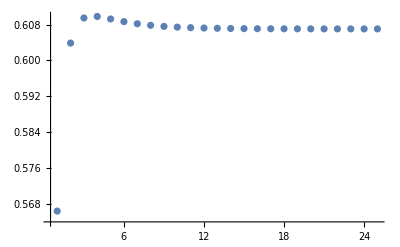

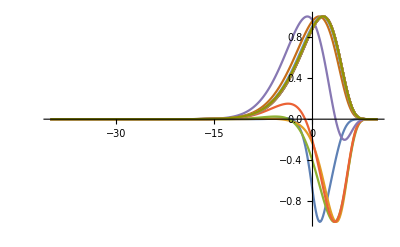

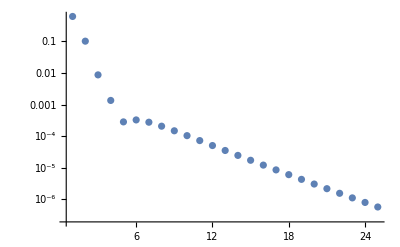

```mathematica
ListPlot[Pite,PlotRange->All]
ListPlot[dsol,PlotRange->All,Joined->True]
ListLogPlot[dmaxite,PlotRange->All]
```

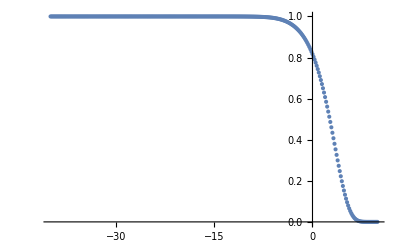

```mathematica
ListPlot[Table[{t,N[ψ[t]]},{t,-Lm,LM,dt}],PlotRange->All]
```

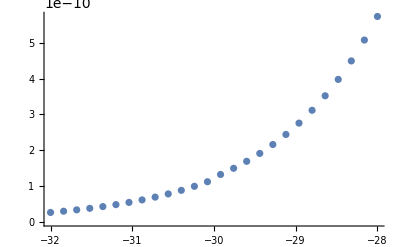

```mathematica
ListPlot[Table[{tt,1-ψ[tt]},{tt,-32,-28,dt}],Joined->False,
PlotRange->All]
```

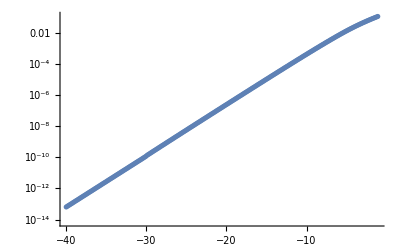

```mathematica
ListLogPlot[Table[{tt,1-ψ[tt]},{tt,-40,-1,dt}],Joined->False,
PlotRange->All]
```

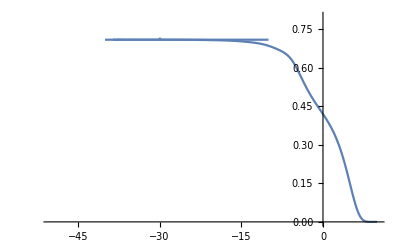

```mathematica
sol=Table[{tt,1.-ψ[tt]},{tt,-Lm,LM,dt}];
Show[ListPlot[Table[{sol[[i,1]],(sol[[i,2]]-sol[[i-1,2]])/dt/sol[[i,2]]},{i,10,Length[sol]}],Joined->True,PlotRange->{{-50,10},{0,.8}}],Plot[(1-E^(-b dt))/dt,{x,-40,-10}]]
```

```mathematica
(* non è chiaro questa soluzione cos'è e come converge al valore limite *)
```

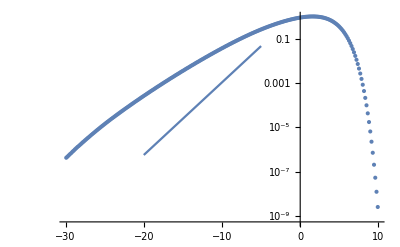

```mathematica
Show[ListLogPlot[Last[dsol]],LogPlot[2. E^(b zz),{zz,-20,-5}]]
```

```mathematica
b
```

0.753016

```mathematica
(**********************************************)
(*************************************************)(*************************************************)(*************************************************)(*************************************************)
```

```mathematica
(*  Soluzione della linearizzata H=0 con comportamento  E^((1-b)t)  *)
```

```mathematica
(**********************************************)(*************************************************)(*************************************************)(*************************************************)(*************************************************)(*************************************************)
```

```mathematica
(*  *)
(* prima devi girare la soluzione ad H=0, poi usa gli stessi parametri della soluzione *)

b=0.753015924638048;
(* condizione iniziale *)
Do[ndψ[tt]=Chop[E^(- E^tt)] E^((1-b) t),{tt,-Lm,LM,dt}];

(* condizione iniziale costante *)

Do[dψ[t]=ndψ[t];,{t,-Lm,LM,dt}];
```

General::munfl: Exp[-827.158] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-970.927] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1139.65] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
IteraSolveD0:=(
dPite={};
dsol={};
dmaxite={};
dmax=1.;
While[dmax>10^-7,

ndψ[-Lm]= .0;
Do[
int=0;
Do[


y=-J (E^(t- tt)+E^(tt- t)) /2(* viene dal limite per H piccolo: tende  a -J Cosh[t-tt] *);

int+=m(J^(1/2)E^J)/(2 π)^(1/2)dψ[tt] ψ[tt]^(m-1) E^(-E^tt) Exp[(t-tt)/2+y];
(* Log[BesselI[1,x]]-x+Log[2π]/2+Log[x]/2 tende a zero per x che diverge, cioe' H piccolo *)
,{tt,-Lm+dt,LM,dt}];
ndψ[t]=  int dt;,{t,-Lm+dt,LM,dt}];

Do[ndψ[t]= E^((1-b) t);,{t,-Lm,-Lm+10,dt}];


Do[diffdψ[t]=dψ[t]-ndψ[t];,{t,-Lm,LM,dt}];


dmax=Max[Table[Abs[diffdψ[t]],{t,-Lm,LM,dt}]];
AppendTo[dsol,Table[{tt,diffdψ[tt]/dmax},{tt,-Lm,LM,dt}]];
AppendTo[dmaxite,dmax];

Do[dψ[t]=ndψ[t];,{t,-Lm,LM,dt}];

dP=0;
Do[dP+=(m+1)dψ[t] ψ[t]^(m+1) E^(- E^t) E^t ,{t,-Lm,LM,dt}];
dP*=(dt); (* controllare la formula, manca un pezzo che dovrebbe dare correzioni regolari in H  *)
AppendTo[dPite,dP];


])
```

```mathematica
IteraSolveD0[];
```

General::munfl: 0.0000799643 1.84678×10^-304 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-819.774] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-961.053] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
lisdψ0=Table[{t,N[dψ[t]]},{t,-Lm,LM,dt}];
```

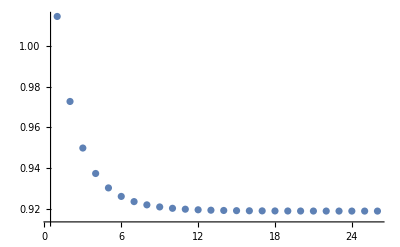

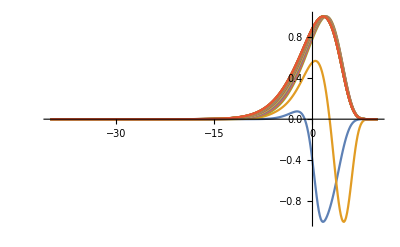

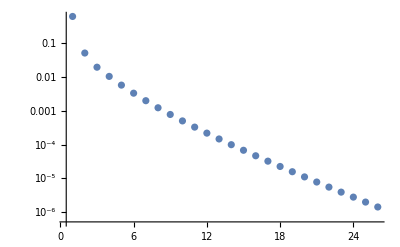

```mathematica
ListPlot[dPite,PlotRange->All]
ListPlot[dsol,PlotRange->All,Joined->True]
ListLogPlot[dmaxite,PlotRange->All]
```

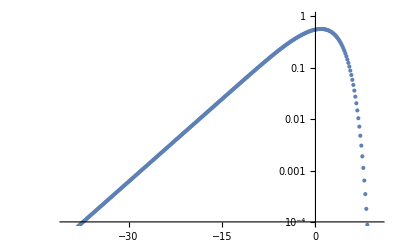

```mathematica
ListLogPlot[Table[{t,N[dψ[t]]},{t,-Lm,LM,dt}],PlotRange->{{-40,10},{.0001,1}}]
```

```mathematica
(******************************************************)
```

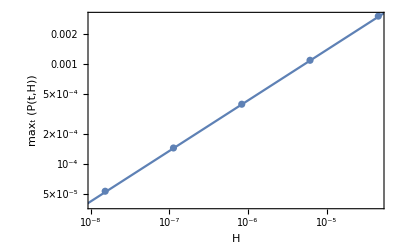

```mathematica
Show[ListLogLogPlot[lismax,Frame->True,FrameLabel->{Style["H",Italic],Style["max_t (P(t,H))",Italic]}],LogLogPlot[c cc /ccc h^(2b-1),{h,10^-9,10^-4}]]
```

```mathematica
ccc=1/mm;
```

```mathematica
cc
```

0.969181

```mathematica
(******************************************************)
(******************************************************)(******************************************************)(******************************************************)(******************************************************)(******************************************************)
```

```mathematica
(********************* Caso Critico **********************************)
```

```mathematica
(** parametri equazioni *)
m=2;

dtt=0.08; (* dt target *)

(* parametri soluzione numerica *)

(* NN=100; *) 

Lm=30;
LM=10;

NN=IntegerPart[Lm/dtt] (* prendo NN in modo da avviciarmi al dt target *)

dt=Lm/NN; (* fondamentale deve essere un razionale, altrimenti non funziona come indici !!!! *)
N[dt]

H=N[E^-Lm]
J=0.026540159736761493;  (* valore critico *)


(* condizione iniziale *)
Do[nψ[tt]= E^(H/(m-1))Chop[E^(- E^tt)],{tt,-Lm,LM,dt}];

(* condizione iniziale costante *)
(*
Do[nψ[tt]= E^(H/(m-1))1.,{tt,-Lm,LM,dt}];
Do[nψ[tt]= 0.,{tt,-Lm,LM,dt}];
*)
Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];
```

375

0.08

9.35762×10^-14

General::munfl: Exp[-765.095] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-828.818] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-897.847] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
IteraSolve[];
```

General::munfl: Exp[-744.466] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-806.071] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-872.803] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
hai dal 22 al 30 con il nuovo codice
```

```mathematica
(* stai girando il 30...
```

```mathematica
(* vedi come viene ma forse l'estrazione del massimo va fatta con più cautela, è meglio prendere quello estrapolato *)
```

```mathematica
lisψ30p08cri=Table[{t,N[ψ[t]]},{t,-Lm,LM,dt}];
```

```mathematica
ListPlot[dsol,PlotRange->All,Joined->True]
```

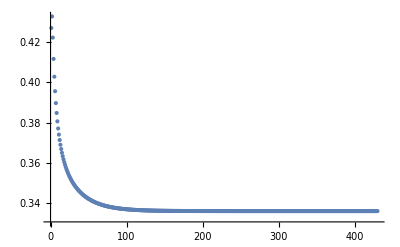

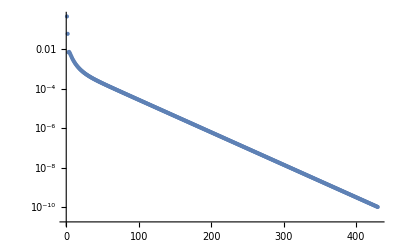

```mathematica
ListPlot[Pite,PlotRange->All]
ListLogPlot[dmaxite,PlotRange->All]
```

```mathematica
(* la convergenza nel caso critico è lenta, ci vogliono molte iterazioni *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tommasorizzo/Dropbox/fisica/N ORBIT

```mathematica
(*
lisψ0crit>>lisψ0crit;
lisψ30p08cri>>lisψ30p08cri;
lisψ28p08cri>>lisψ28p08cri;
lisψ26p08cri>>lisψ26p08cri;
lisψ24p08cri>>lisψ24p08cri;
lisψ22p08cri>>lisψ22p08cri;
lisψ20p08cri>>lisψ20p08cri;
lisψ18p08cri>>lisψ18p08cri;
lisψ16p08cri>>lisψ16p08cri;
lisψ14p08cri>>lisψ14p08cri;
```

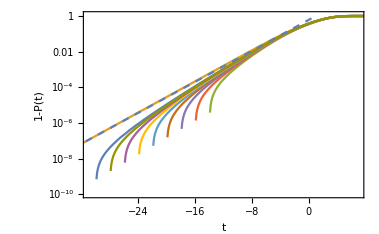

```mathematica
Show[ListLogPlot[{Map[{#[[1]],1-#[[2]]}&,Table[{t,N[ψ[t]]},{t,-Lm,LM,dt}]],Map[{#[[1]],1-#[[2]]}&,lisψ0crit],Map[{#[[1]],1-#[[2]]}&,lisψ14p08cri],Map[{#[[1]],1-#[[2]]}&,lisψ16p08cri],Map[{#[[1]],1-#[[2]]}&,lisψ18p08cri],Map[{#[[1]],1-#[[2]]}&,lisψ20p08cri],Map[{#[[1]],1-#[[2]]}&,lisψ22p08cri],Map[{#[[1]],1-#[[2]]}&,lisψ24p08cri],Map[{#[[1]],1-#[[2]]}&,lisψ26p08cri],Map[{#[[1]],1-#[[2]]}&,lisψ28p08cri]},PlotRange->{{-31,7},{10^-10,1.1}},Joined->True,Frame->True,FrameLabel->{Style["t",Italic],Style["1-P(t)",Italic]}],LogPlot[.61 E^(0.5  t),{t,-40,1},PlotStyle->{Dashed}]]
```

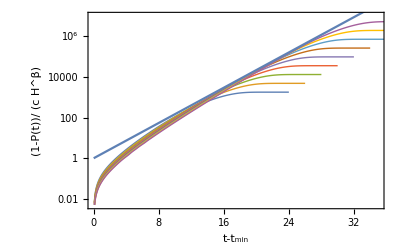

```mathematica
Show[ListLogPlot[{Map[{#[[1]]+14,(1-#[[2]])/(c E^(-14 b))}&,lisψ14p08cri],Map[{#[[1]]+16,(1-#[[2]])/(c E^(-16 b))}&,lisψ16p08cri],Map[{#[[1]]+18,(1-#[[2]])/(c E^(-18 b)) }&,lisψ18p08cri],Map[{#[[1]]+20,(1-#[[2]])/(c E^(-20 b)) }&,lisψ20p08cri],Map[{#[[1]]+22,(1-#[[2]])/(c E^(-22 b)) }&,lisψ22p08cri],Map[{#[[1]]+24,(1-#[[2]])/(c E^(-24 b)) }&,lisψ24p08cri],Map[{#[[1]]+26,(1-#[[2]])/(c E^(-26 b)) }&,lisψ26p08cri],Map[{#[[1]]+28,(1-#[[2]])/(c E^(-28 b)) }&,lisψ28p08cri],Map[{#[[1]]+30,(1-#[[2]])/(c E^(-30 b)) }&,lisψ30p08cri]},PlotStyle->{Thick,Thick,Thick},PlotRange->{{0,35},{.005,10000000}},Joined->True,Frame->True,FrameLabel->{Style["t-t_min",Italic],Style["(1-P(t))/ (c H^β)",Italic]}],LogPlot[E^(b t),{t,0 ,35}]]
```

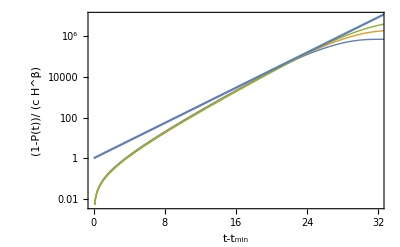

```mathematica
Show[ListLogPlot[{Map[{#[[1]]+26,(1-#[[2]])/(c E^(-26 b)) }&,lisψ26p08cri],Map[{#[[1]]+28,(1-#[[2]])/(c E^(-28 b)) }&,lisψ28p08cri],Map[{#[[1]]+30,(1-#[[2]])/(c E^(-30 b)) }&,lisψ30p08cri]},PlotStyle->{Thick,Thick,Thick},PlotRange->{{0,32},{.005,10000000}},Joined->True,Frame->True,FrameLabel->{Style["t-t_min",Italic],Style["(1-P(t))/ (c H^β)",Italic]}],LogPlot[E^(b t),{t,0 ,35}]]
```

```mathematica
OK, sembra che solo a 20 arriva sulla curva, d'altra parte l'altro ci arriva solo intorno a -5 è per questo che devi arrivare a questi valori...
```

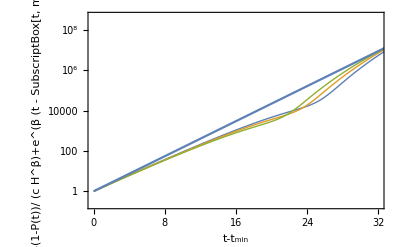

```mathematica
Show[ListLogPlot[{Map[{#[[1]]+30,-(1-#[[2]])/(c E^(-30 b))+E^(b (#[[1]]+30)) }&,lisψ30p08cri],Map[{#[[1]]+28,-(1-#[[2]])/(c E^(-28 b))+E^(b (#[[1]]+28)) }&,lisψ28p08cri],Map[{#[[1]]+26,-(1-#[[2]])/(c E^(-26 b))+E^(b (#[[1]]+26)) }&,lisψ26p08cri]},PlotStyle->{Thick,Thick,Thick},PlotRange->{{0,32},Automatic},Joined->True,Frame->True,FrameLabel->{Style["t-t_min",Italic],Style["-(1-P(t))/ (c H^β)+e^(β (t - SubscriptBox[t, min]))",Italic]}],LogPlot[E^(b t),{t,0 ,35}]]
```

```mathematica
(*******************************************************)
(*******************************************************)
(******** differenza con la soluzione a H=0 ************)
(*******************************************************)
(*******************************************************)
(*******************************************************)
```

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

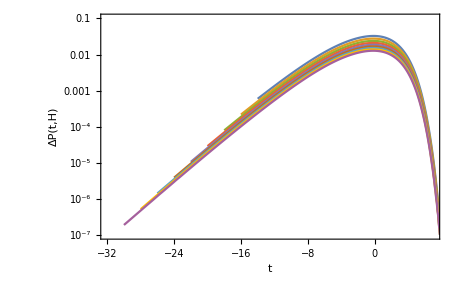

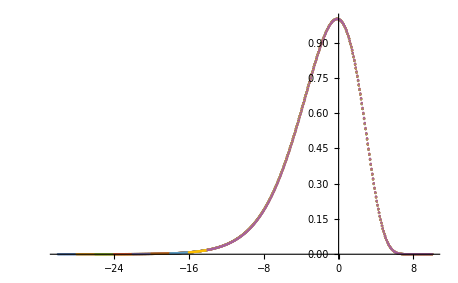

```mathematica
lismax={}; (* ATTENZIONE non è il massimo, è il valore in zero *)



lis=lisψ30p08cri;
d30=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[ lisψ0crit ][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d30;
mm=Max[Map[#[[2]]&,dd]];
mm=Interpolation[dd][0.];  (* faccio un'interpolazione è più precisa *)
AppendTo[lismax,{E^-30,mm}];
sd30=Map[{#[[1]],#[[2]]/mm}&,dd];






lis=lisψ28p08cri;
d28=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[ lisψ0crit ][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d28;
mm=Max[Map[#[[2]]&,dd]];
mm=Interpolation[dd][0.];  (* faccio un'interpolazione è più precisa *)
AppendTo[lismax,{E^-28,mm}];
sd28=Map[{#[[1]],#[[2]]/mm}&,dd];






lis=lisψ26p08cri;
d26=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[ lisψ0crit ][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d26;
mm=Max[Map[#[[2]]&,dd]];
mm=Interpolation[dd][0.];  (* faccio un'interpolazione è più precisa *)
AppendTo[lismax,{E^-26,mm}];
sd26=Map[{#[[1]],#[[2]]/mm}&,dd];



lis=lisψ24p08cri;
d24=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[ lisψ0crit ][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d24;
mm=Max[Map[#[[2]]&,dd]];
mm=Interpolation[dd][0.];  (* faccio un'interpolazione è più precisa *)
AppendTo[lismax,{E^-24,mm}];
sd24=Map[{#[[1]],#[[2]]/mm}&,dd];




lis=lisψ22p08cri;
d22=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[ lisψ0crit ][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d22;
mm=Max[Map[#[[2]]&,dd]];
mm=Interpolation[dd][0.];  (* faccio un'interpolazione è più precisa *)
AppendTo[lismax,{E^-22,mm}];
sd22=Map[{#[[1]],#[[2]]/mm}&,dd];




lis=lisψ20p08cri;
d20=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[ lisψ0crit ][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d20;
mm=Max[Map[#[[2]]&,dd]];
mm=Interpolation[dd][0.];  (* faccio un'interpolazione è più precisa *)
AppendTo[lismax,{E^-20,mm}];
sd20=Map[{#[[1]],#[[2]]/mm}&,dd];




lis=lisψ18p08cri;
d18=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[ lisψ0crit ][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d18;
mm=Max[Map[#[[2]]&,dd]];
mm=Interpolation[dd][0.];  (* faccio un'interpolazione è più precisa *)
AppendTo[lismax,{E^-18,mm}];
sd18=Map[{#[[1]],#[[2]]/mm}&,dd];

lis=lisψ16p08cri;
d16=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[lisψ0crit][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d16;
mm=Max[Map[#[[2]]&,dd]];
mm=Interpolation[dd][0.];  (* faccio un'interpolazione è più precisa *)
AppendTo[lismax,{E^-16,mm}];
sd16=Map[{#[[1]],#[[2]]/mm}&,dd];


lis=lisψ14p08cri;
d14=Table[{lis[[i,1]],lis[[i,2]]-Interpolation[lisψ0crit][lis[[i,1]]]},{i,1,Length[lis]}];

dd=d14;
mm=Max[Map[#[[2]]&,dd]];
mm=Interpolation[dd][0.];  (* faccio un'interpolazione è più precisa *)
AppendTo[lismax,{E^-14,mm}];
sd14=Map[{#[[1]],#[[2]]/mm}&,dd];


ListLogPlot[{d14,d16,d18,d20,d22,d24,d26,d28,d30},PlotRange->{{-32,7},{ 10^-7,.1}},Joined->True,Frame->True,FrameLabel->{Style["t",Italic],Style["ΔP(t,H)",Italic]}]
ListPlot[{sd30,sd28,sd26,sd24,sd22,sd20,sd18,sd16,sd14},PlotRange->All]
```

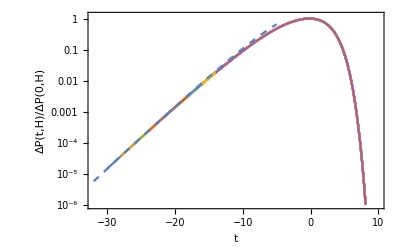

```mathematica
Show[ListLogPlot[{sd30,sd28,sd26,sd24,sd22,sd20,sd18,sd16,sd14},PlotRange->{{-32,10},{.000001,1.2}},Joined->True,Frame->True,FrameLabel->{Style["t",Italic],Style["ΔP(t,H)/ΔP(0,H)",Italic]}],LogPlot[-zz 1.6 E^(.5 zz),{zz,-32,-5},PlotStyle->Dashed]]
```

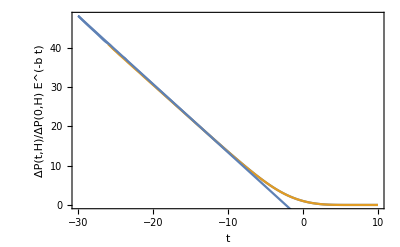

```mathematica
Show[ListPlot[{Map[{#[[1]],#[[2]] E^(-b #[[1]])}&,sd30],Map[{#[[1]],#[[2]] E^(-b #[[1]])}&,sd26]},PlotRange->Automatic,Joined->True,Frame->True,FrameLabel->{Style["t",Italic],Style["ΔP(t,H)/ΔP(0,H) E^(-b t)",Italic]}],Plot[-1.74t-4.,{t,-30,0}]]
```

```mathematica
(* non c'è dubbio che l'andamento sia quello *)
```

```mathematica
m L(t-t')E^(β t')dt'=E^(β t)m L(t-t')E^(β t'-β t)dt'= E^(β t)(m L(t-t')E^(β t'-β t)dt')

m L(t-t')t' E^(β t')dt'=E^(β t)m L(t-t')E^(β t'-β t)(t'-t)dt'+t (E^(β t)m L(t-t')E^(β t'-β t))= E^(β t)(m L(t-t')E^(β t'-β t)(t'-t)dt')+ t E^(β t)
```

```mathematica
ora vale
```

```mathematica
L(t-t')=E^((t-t')/2-J Cosh[t-t'])
```

```mathematica
ed esattamente al punto critico dove β=1/2
```

```mathematica
L(t-t')E^(β t'-β t)
```

```mathematica
diventa simmetrica rispetto a (t-t') e in questo modo il termine proporzionale a  E^(β t)  si annulla.
quindi al punto critico esiste una soluzione che decade come t E^(β t), bisogna poi trovare questa soluzione  e vedere come si comporta cioè come la convergenza asintotica, sicuramente c'è una correzione in   E^(β t) , non so da chi è determinata
```

```mathematica
questa soluzione è quella che c'è ad ogni beta per l'operatore
```

```mathematica
se metti che
```

```mathematica
c E^(β Subscript[t, min])+ xx Subscript[t, min] E^(β Subscript[t, min])==0
```

```mathematica
segue che  xx = c/Subscript[t, min]
```

```mathematica
c E^(β Subscript[t, min]+β Δt)+ xx Subscript[t, min] E^(β Subscript[t, min]+β Δt)+xx Δt E^(β Subscript[t, min]+β Δt) = xx Δt E^(β Subscript[t, min]+β Δt)
```

```mathematica
(* ma questo non mi convince molto *)
```

```mathematica
(* devi studiare la soluzione da sotto come si comporta *)
```

```mathematica
(* in effetti il matching è complicato però puoi cercare la soluzione da sotto vedendo se la riesci a trovare senza fissare le condizioni*)
```

```mathematica
(* c'è comunque una funzione unica (da trovare) e il decadimento è molto lento *)
```

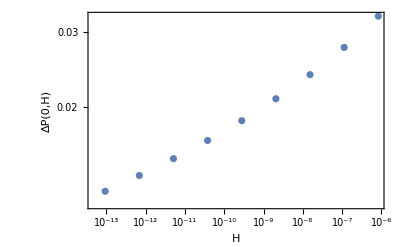

```mathematica
ListLogLogPlot[lismax,Frame->True,FrameLabel->{Style["H",Italic],Style["ΔP(0,H)",Italic]}]
```

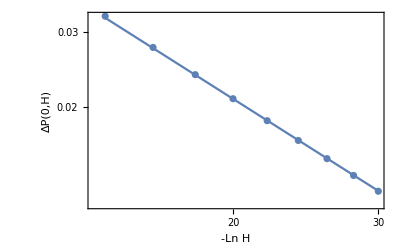

```mathematica
Show[ListLogLogPlot[Map[{-Log[#[[1]]],#[[2]]}&,lismax],Frame->True,FrameLabel->{Style["-Ln H",Italic],Style["ΔP(0,H)",Italic]}],LogLogPlot[Exp[-0.19917289566394591-1.2240603644051458Log[mlh]],{mlh,14,30}]]
```

```mathematica
Fit[Take[Map[{Log[-Log[#[[1]]]],Log[#[[2]]]}&,lismax],2],{1,xx},xx]
```

-0.176389-1.23131 xx

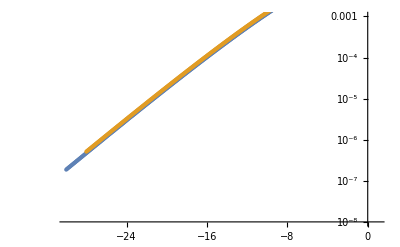

```mathematica
ListLogPlot[{d30,d28},PlotRange->{{-30,1},{10^-8,.001}}]
```

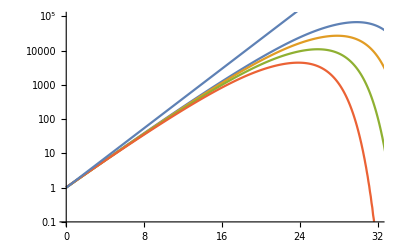

```mathematica
Show[ListLogPlot[{Map[{#[[1]]+30,#[[2]]/(c E^(-b 30))}&,d30],Map[{#[[1]]+28,#[[2]]/(c E^(-b 28))}&,d28],Map[{#[[1]]+26,#[[2]]/(c E^(-b 26))}&,d26],Map[{#[[1]]+24,#[[2]]/(c E^(-b 24))}&,d24]},PlotRange->{{0,32},{.1,100000}},Joined->True],LogPlot[{E^(t/2)},{t,0,30}]]
```

```mathematica
(* la correzione è molto grande e decade molto lentamente *)
```

```mathematica
(* bisogna studiare le due funzioni linearizzate, proviamo prima quella vicino a Subscript[t, min] *)
```

```mathematica
(************************************************)
(************************************************)(************************************************)(******************** SOluzione H=0 critica ****************************)(************************************************)(************************************************)(************************************************)
```

```mathematica
(************************************************)
```

```mathematica
(** parametri equazioni *)
m=2;


(* parametri soluzione numerica *)

Lm=40;
LM=10;

NN=250; 

dt=Lm/NN; (* fondamentale deve essere un razionale, altrimenti non funziona come indici !!!! *)
N[dt]


J=0.026540159736761493;  


(* condizione iniziale *)
Do[nψ[tt]=Chop[E^(- E^tt)],{tt,-Lm,LM,dt}];

(* condizione iniziale costante *)

Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];
```

0.16

```mathematica
b=0.5;
c=0.61;

IteraSolve0[];
```

General::munfl: Exp[-710.129] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-832.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-976.047] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
lisψ0crit=Table[{t,N[ψ[t]]},{t,-Lm,LM,dt}];
```

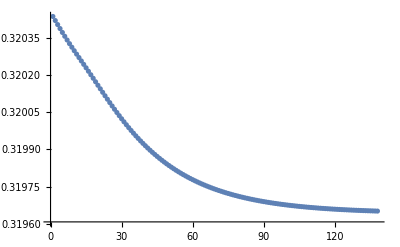

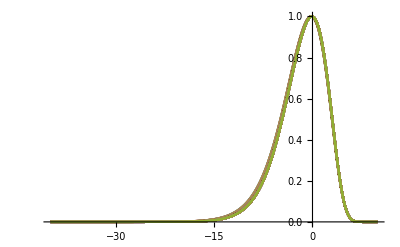

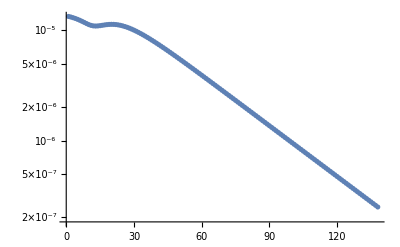

```mathematica
ListPlot[Pite,PlotRange->All]
ListPlot[dsol,PlotRange->All,Joined->True]
ListLogPlot[dmaxite,PlotRange->All]
```

```mathematica
ListPlot[Table[{t,N[ψ[t]]},{t,-Lm,LM,dt}],PlotRange->All]
```

-Graphics-

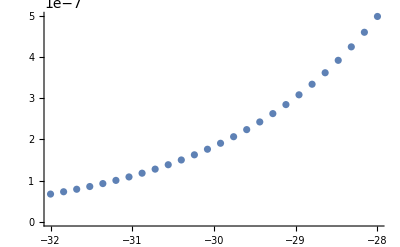

```mathematica
ListPlot[Table[{tt,1-ψ[tt]},{tt,-32,-28,dt}],Joined->False,
PlotRange->All]
```

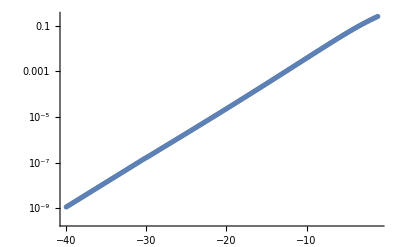

```mathematica
ListLogPlot[Table[{tt,1-ψ[tt]},{tt,-40,-1,dt}],Joined->False,
PlotRange->All]
```

```mathematica
b
```

0.5

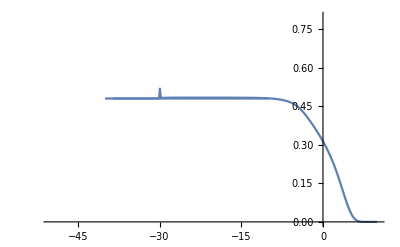

```mathematica
sol=Table[{tt,1.-ψ[tt]},{tt,-Lm,LM,dt}];
Show[ListPlot[Table[{sol[[i,1]],(sol[[i,2]]-sol[[i-1,2]])/dt/sol[[i,2]]},{i,10,Length[sol]}],Joined->True,PlotRange->{{-50,10},{0,.8}}],Plot[(1-E^(-b dt))/dt,{x,-40,-10}]]
```

```mathematica
(************************************************)
(************************************************)(************************************************)(******************** ****************************)(************************************************)(************************************************)(************************************************)
```

```mathematica
(************Soluzione linearizzata vicino a Subscript[t, min]**************+)
```

```mathematica
(** parametri equazioni *)
m=2;

(* parametri soluzione numerica *)

Lm=0; 
H=N[E^-Lm]; (* il campo è come se fosse uno *)
LM=100;
Δ=90;  (* valore oltre il quale impongo che la soluzione vada come E^(b tt) *)

NN=250; 

dt=LM/NN; (* fondamentale deve essere un razionale, altrimenti non funziona come indici !!!! *)
N[dt]

J=0.026540159736761493;  (* valore critico *)

b=0.5;
cc=0.; (* questo lo devi mettere perchè c'è nella funzione IteraSolveLin[] *)


(* condizione iniziale OK  *)
Do[nψ[tt]=E^(b tt),{tt,-Lm,LM,dt}];
Do[ψ[t]=nψ[t];,{t,-Lm,LM,dt}];
```

0.4

```mathematica
lisψlin0crit=Table[{tt,ψ[tt]},{tt,Lm,LM,dt}];
```

```mathematica
IteraSolveLin[];
```

General::munfl: Exp[-752.223] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1119.73] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1667.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

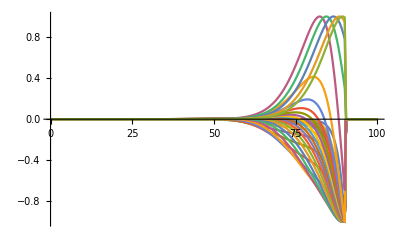

```mathematica
ListPlot[dsol,PlotRange->All,Joined->True]
```

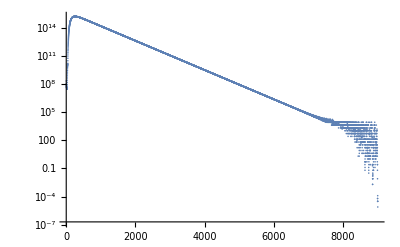

```mathematica
ListLogPlot[dmaxite,PlotRange->All]
```

```mathematica
(* devi accelerare la convergenza *)
```

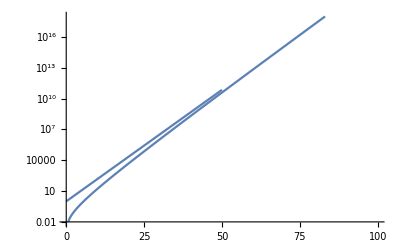

```mathematica
Show[ListLogPlot[Table[{tt,ψ[tt]},{tt,Lm,LM,dt}],Joined->True,PlotRange->{.01,1000^6}],LogPlot[E^(b x),{x,0,50}]]
```

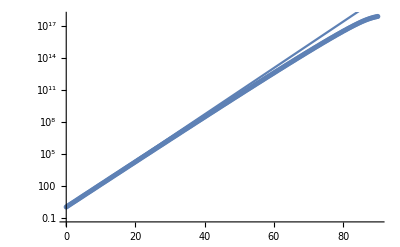

```mathematica
Show[ListLogPlot[Table[{tt,E^(b tt)-ψ[tt]},{tt,Lm,LM,dt}]],LogPlot[E^(b t),{t,0,100}]]
```

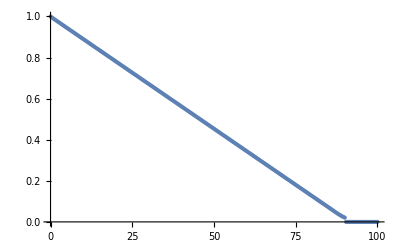

```mathematica
ListPlot[Table[{tt,(E^(b tt)-ψ[tt])/E^(b tt)},{tt,Lm,LM,dt}],PlotRange->All]
```

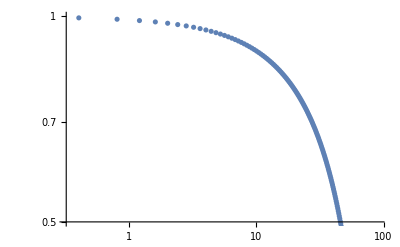

```mathematica
ListLogLogPlot[Table[{tt,(E^(b tt)-ψ[tt])/E^(b tt)},{tt,Lm,LM,dt}],PlotRange->{.5,1}]
```

```mathematica
forse c'è una correzione logaritmica, comunque la correazione cresce  devi vedere la questione dell'operatore che ha i t/2  sempre e quindi potrebbe giocare un ruolo al punto critico...
```

```mathematica
difficile
```